# Term Project

### Project Proposal

1. Our project will be to create a 3D simulation that models launching an object from the earth into space and plotting its trajectory, as well as the landing location, if it does land. We plan on starting with just a simulation of launching the object and it coming back to earth so we can understand how to represent the simplest form of projectile motion. When we finish this, we will consider how to launch the object in such a way that it will reach the point at which it would start orbiting the earth. We will then consider additional components in our calculations like air resistance, how long the force of thrust should be applied, how using fuel changes the situation (i.e. the mass of the object changes as fuel is expended), and other components that we haven’t yet accounted for. Our goal is to create a module that produces a 3D graph plotting the trajectory of the projectile around the earth given certain input parameters.

2. To start, we will split up the research into the components listed above. Nicolas will investigate the relationship between fuel consumption and force, while Jason will research how to treat air resistance considering the changing density of the atmosphere with altitude. Both of us will look into the formulas behind projectile motion and objects orbiting the earth because neither of us are completely familiar with those topics. The first major milestone will be to create a 2D graph of projectile motion. The second major milestone will be to create a 2D graph of orbital motion around the earth. From there, we will model the same situations in 3D. Finally, we will individually add in the components we were each responsible for researching (fuel consumption, air resistance).

3. Our project will require analysis in the following areas: projectile motion, orbital motion/mechanics, air resistance, and the relationship between the mass of the fuel and the thrust it can provide. We will need to thoroughly understand how to create 3D graphs in Mathematica. These graphs will probably require space curves. We will analyze how each of the “additional” components we consider (air resistance, fuel/mass relationship, etc) interact with the other components, if they do. We will also need to make sure that our graph clearly shows where the object is as a function of time.

4. Problems could arise if we mix up variables in our code or we don’t correctly incorporate certain factors, meaning we misunderstand how one component impacts the other components. An example of this would be forgetting to account for the change in mass of the object/rocket as fuel is used up to enable thrust against the force of gravity, which changes with distance from the earth. Many other important issues we will need to carefully address are related to the 3D graph. How will we make the graph a function of time instead of space? How will we represent unsuccessful orbital paths on the graph? Can we model several paths at once? How will we model the earth and objects hitting the surface of the earth? We will need to ensure that the scale of the graph is such that the graph is useful and readable.

### First Milestone

The first major milestone will be to create a 2D graph of projectile motion.

We would be animating one object which is the projectile. One axis would be the ground and the other axis would be the height above the ground. We are hoping for it to include the past positions of where the object was.

```mathematica
freefallStage[initialPosx_,initialPosy_,initialVelx_,initialVely_,mass_]:=Module[{force,acc,vel,pos,t,timeToGround,pathPlot,animateTime,pathAnimation,g =-9.8},
(*set up the equations we will need. force and acc are constant but vel and pos are functions of t*)
force={0,mass*g}; (*because the projectile is in freefall*) 
acc[t_]=force/mass;
vel[t_]={initialVelx,initialVely}+Integrate[acc[t],t];
pos[t_]={initialPosx,initialPosy}+Integrate[vel[t],t];

(*calculate the time it will take the projectile to reach the ground, where the y component of position is less than 0*)
timeToGround=t/.FindRoot[pos[t][[2]]==0,{t,100}];(*Current issue: how can we reliably find the positive root, not the negative one?*)

(*set up the parametric plot*)
pathPlot=ParametricPlot[pos[t],{t,0,timeToGround},PlotStyle->{Red, Dashed},AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeToGround]];

Animate[Show[pathPlot,Graphics[Point[pos[t]]]],{t,0,timeToGround}]

(*We could try animating using the way described in that lab, by creating a list of frames and then combining them, instead of using the animate command directly*)

(*pathAnimation=Table[pathPlot,{animateTime,0,timeToGround,0.05}];
Animate[pathAnimation,{animateTime,0,timeToGround}]*)
]
freefallStage[10,10,6,5,50]
```

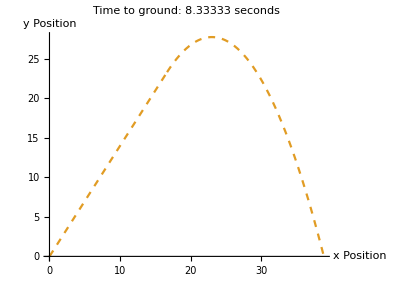

```mathematica
twoStage[thrustx_,thrusty_,timeThrustApplied_,mass_]:=Module[{force,acc,vel,pos,t,timeToGround,thrustPlot,freefallPlot,g=-9.8},
(*thrust stage*)
force={thrustx,thrusty+mass*g};
acc=force/mass;
vel={0,0}+Integrate[acc,t]; (*No initial velocity*)
pos={0,0}+Integrate[vel,t];

(*set up the parametric plot*)
thrustPlot=ParametricPlot[pos,{t,0,timeThrustApplied},PlotStyle->{Red, Dashed}];

(*freefall stage*)
force={0,mass*g}; (*because the projectile is in freefall*) 
acc=force/mass;
vel=(vel/.t->timeThrustApplied)+Integrate[acc,t];
pos=(pos/.t->timeThrustApplied)+Integrate[vel,t];

(*calculate the time it will take the projectile to reach the ground, where the y component of position is less than 0*)
timeToGround=t/.FindRoot[pos[[2]]==0,{t,100}];(*Current issue: how can we reliably find the positive root, not the negative one?*)

(*set up the parametric plot*)
freefallPlot=ParametricPlot[pos,{t,0,timeToGround},PlotStyle->{Red, Dashed}];

(*Show the final plot*)
Show[{thrustPlot,freefallPlot},PlotRange->All,AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeThrustApplied+timeToGround]]
]
twoStage[4,35,5,3]
```

### Second Milestone

The second major milestone will be to create a 2D graph of orbital motion around the earth. 
Two objects will be animated, where one is the earth, which wouldn’t move. The second would be the rocket’s position. For this one, the plot will be on an {x,y} axis with the time factor changing.